{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

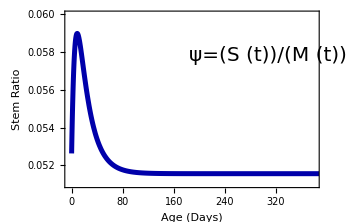

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;d=0.05;m=1000;
s=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))* (v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==112.6,M[0]==2139.4},{S,M},{x,0,900}]
g1s=Plot[Evaluate[(*v0+v1/(1+{{M[x]}/.s}/m)*){{0.002*{S[x]}/.s}}/{{0.002*{M[x]}/.s}}],{x,0,900},PlotRange->{{-3,380},{0.051,0.06}},PlotStyle->{Darker[Blue],Thickness[0.01]},(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,(*FrameLabel->{"Age (days)","Growth Ratio"}*)FrameLabel->{Style["Age (Days)",18(*,Bold*)],Style["Stem Ratio",18(*,Bold*)]}(*,FrameStyle->Directive[Black,12]*)(*,PlotLabel->"(A)"*),FrameTicks->{Automatic},FrameTicksStyle->Directive[Black,14], LabelStyle->Directive[(*Bold,*)Black,14,FontFamily->"Times New Roman"],Epilog->Text[Style["ψ=(S (t))/(M (t))",Black,(*Bold,Italic*)20,FontFamily->"Times New Roman"],Scaled[{.8,.75}]]]
(*g1=Plot[Evaluate[(*v0+v1/(1+{{M[x]}/.s}/m)*){{0.002*{S[x]}/.s}}],{x,0,900},PlotRange->{{0,100},{0.15,0.6}},PlotStyle->Purple,(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True,FrameLabel->{"Time (days)","Stem cell growth (grams)"},FrameStyle->Directive[Black,12],LabelStyle->Directive[Bold,Black]]*)
(*pl1=Labeled[g1,Style["(A)","Section",Black],{{Top,Left}}]*)
```

```mathematica
(*For[x=0,x≤500,x+=1,

Print[x,"  ",((S[x]/.s)/(M[x]/.s))[[1]],"    ",(S[x]/.s)[[1]],"    ",(M[x]/.s)[[1]]]]*)
```

```mathematica
g2=Plot[Evaluate[(*v0+v1/(1+{{M[x]}/.s}/m)*){{0.002*{M[x]}/.s}}/{{0.002*{S[x]}/.s}}],{x,0,900},PlotRange->{{0,380},{16.7,19.5}},PlotStyle->Darker[Blue],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)(*PlotLegends->{"Healthy growth"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,Frame->True(*,PlotLabel->"(B)"*),FrameLabel->{"Age (days)","Growth Ratio"},FrameStyle->Directive[Black,12],LabelStyle->Directive[(*Bold,*)Black],Epilog->Text[Style["ψ^-1=(M (t))/(S (t))",Black,(*Bold,Italic*)18],Scaled[{.8,.75}]]];
```

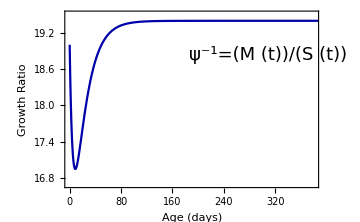
-Graphics-(B)

```mathematica
pl2=Labeled[g2,Style["(B)","Section",Black],{{Top,Left}}]
```

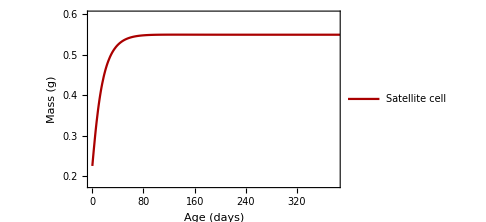

```mathematica
g3=Plot[Evaluate[(*v0+v1/(1+{{M[x]}/.s}/m)*){{0.002*{S[x]}/.s}}],{x,0,900},PlotRange->{{0,380},{0.18,0.6}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)AxesStyle->Directive[Black,12],ImageSize->Medium,(*Frame->True,FrameLabel->{"Time (days)","Stem cell growth (grams)"},FrameStyle->Directive[Black,12],*)(*LabelStyle->Directive[Bold,Black],AxesLabel->{"Age (days)","Mass (g)"},*)Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Mass (g)",None},{"Age (days)",None}},FrameStyle->Directive[Black,12],LabelStyle->Directive[(*Bold,*)Black],PlotLegends->Placed[{"Satellite cell"},{0.5,0.5}]]
```

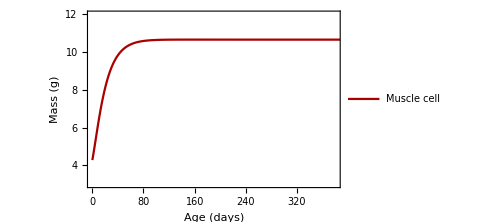

```mathematica
g4=Plot[Evaluate[(*v0+v1/(1+{{M[x]}/.s}/m)*){{0.002*{M[x]}/.s}}],{x,0,900},PlotRange->{{0,380},{3,12}},PlotStyle->Darker[Red],(*AxesLabel->{"Time (days)","ν_0+ν_1/(1+M[mm^3]/m)"},*)PlotLegends->Placed[{"Muscle cell"},{0.5,0.5}],AxesStyle->Directive[Black,12],ImageSize->Medium,(*Frame->True,FrameLabel->{"Time (days)","Stem cell growth (grams)"},FrameStyle->Directive[Black,12],*)Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Mass (g)",None},{"Age (days)",None}},FrameStyle->Directive[Black,12],LabelStyle->Directive[(*Bold,*)Black]]
```

```mathematica
(*d1=GraphicsGrid[{{pl1,g3},{pl2,g4}}]*)
```

```mathematica
Export["D:/g1.eps",g1s]
```

D:/g1.eps

```mathematica
Export["D:/g2.eps",pl2]
Export["D:/g3.eps",g3]
Export["D:/g4.eps",g4]
```

D:/g2.eps

D:/g3.eps

D:/g4.eps